T.X X^(-1)==P X^(-1)→T=P X^(-1)

```mathematica
Train[charaPoints_,anchor_,one_:False]:=Module[{PIX,cp=charaPoints},cp=If[one,#~Join~{1}&/@cp,cp];PIX=PseudoInverse[cpᵀ];Table[anchorᵀ⟦i⟧ᵀ.PIX,{i,1,Length[anchorᵀ]}]]
```

```mathematica
TrainAll[charaPoints_,anchor_,one_:False]:=(Train[#,anchor,one]&/@charaPoints)ᵀ
```

```mathematica
line3=RotationTransform[π/6,{0,0}]/@line1;
graphdata3=Partition[RotationTransform[π/6,{0,0}]/@Flatten[graphdata,1],4];

line4=RotationTransform[-π/6,{0,0}]/@line1;
graphdata4=Partition[RotationTransform[-π/6,{0,0}]/@Flatten[graphdata,1],4];

line5=RotationTransform[π/6,{0,0}]/@line2;
graphdata5=Partition[RotationTransform[π/6,{0,0}]/@Flatten[graphdata2,1],4];

line6=RotationTransform[-π/6,{0,0}]/@line2;
graphdata6=Partition[RotationTransform[-π/6,{0,0}]/@Flatten[graphdata2,1],4];
```

```mathematica
models=Train[Flatten/@{line1,line2,line3,line4,line5,line6},Flatten[#,1]&/@{graphdata,graphdata2,graphdata3,graphdata4,graphdata5,graphdata6},True];
```

```mathematica
RotationTransform[π/6,{0,0}]/@line1
```

{{0.025,-0.0433013},{0.544615,0.256699},{0.00429492,-0.407439},{0.87032,0.092561}}

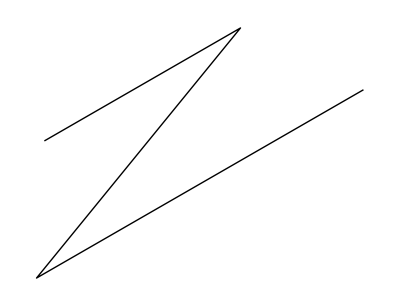

```mathematica
Graphics[Line[RotationTransform[π/6,{0,0}]/@line1]]
```

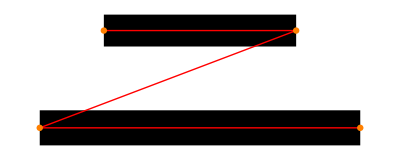

```mathematica
Graphics[{Polygon/@Partition[#.(Flatten[line1]~Join~{1})&/@models,4],Red,Line@line1,Orange,Disk[#,0.01]&/@line1}]
```

```mathematica
line1
```

{{0,-0.05},{0.6,-0.05},{-0.2,-0.355},{0.8,-0.355}}

{{0,0},{0.5,0.},{-0.2,-0.5},{0.7,-0.5}}

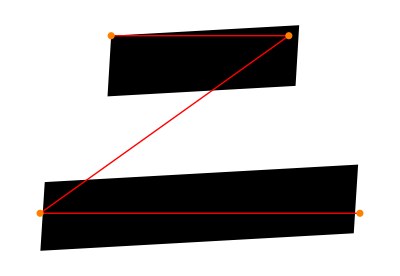

```mathematica
line={{0,0},{0.5,-0.0},{-0.2,-0.5},{0.7,-0.5}}
Graphics[{Polygon/@Partition[#.(Flatten[line]~Join~{1})&/@models,4],Red,Line@line,Orange,Disk[#,0.01]&/@line}]
```

```mathematica
models⟦3⟧//MatrixForm
```

(0.00502133 | 0.0210321 | 0.34477 | -0.0210321 | -0.0997675 | 0.0350534 | 0.466481 | -0.0350534 | 2.22045×10^-16
-0.0210321 | 0.00502133 | 0.0210321 | 0.34477 | -0.0350534 | -0.0997675 | 0.0350534 | 0.466481 | -5.55112×10^-17)

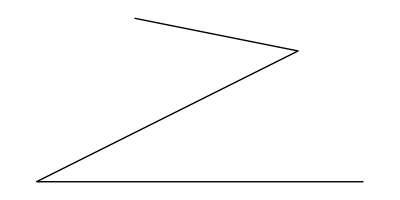

```mathematica
Graphics[Line[line]]
```